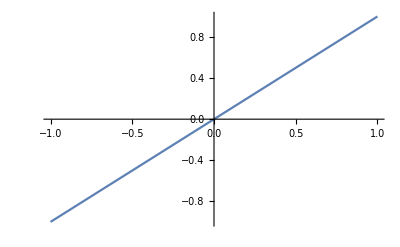

```mathematica
Plot[x,{x,-1,1}]
```

```mathematica
PDF[NormalDistribution[],x]
```

(ⅇ^(-x^2/2))/(√(2 π))

```mathematica
FullForm[Out[2]]
```

Times[Power[E,Times[Rational[-1,2],Power[x,2]]],Power[Times[2,Pi],Rational[-1,2]]]

```mathematica
Sin @* InverseFunction[Sin]
```

Sin@*ArcSin

```mathematica
(Sin @* InverseFunction[Sin])[x]
```

x

```mathematica
expr=Times[Power[E,Times[Rational[-1,2],Power[x,2]]],Power[Times[2,Pi],Rational[-1,2]]]
```

(ⅇ^(-x^2/2))/(√(2 π))

```mathematica
expr//Head
```

Times

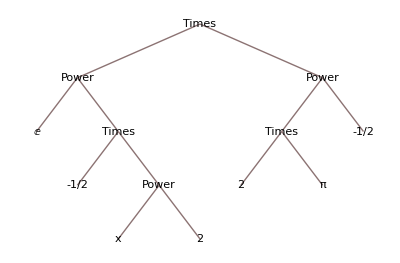

```mathematica
(ⅇ^(-x^2/2))/(√(2 π))//TreeForm
```

```mathematica
First[expr]
```

ⅇ^(-x^2/2)

```mathematica
Times[Power[E,Times[Rational[-1,2],Power[x,2]]],Power[Times[2,Pi],Rational[-1,2]]]
```

(ⅇ^(-x^2/2))/(√(2 π))

```mathematica
Composition[Times[Power[E,Times[Rational[-1,2],Power[x,2]]],Power[Times[2,Pi],Rational[-1,2]]]
```

```mathematica
(ⅇ^(-x^2/2))/(√(2 π))//TreeForm
```

-Graphics-

```mathematica
RightComposition[f,g]
```

f/*g

```mathematica
RightComposition[(#x)^2&,-#/2&,Exp,# Power[2 π,-1/2]&]
```

(#x)^2&/*(-#1/2&)/*Exp/*(#1 (2 π)^(-1/2)&)

```mathematica
RightComposition[#^2&,-#/2&,Exp,# Power[2 π,-1/2]&][x]
```

(ⅇ^(-x^2/2))/(√(2 π))

```mathematica
RightComposition[#^2&,-#/2&,Exp,# Power[2 π,-1/2]&]
```

#1^2&/*(-#1/2&)/*Exp/*(#1 (2 π)^(-1/2)&)

```mathematica
InverseFunction[RightComposition[#^2&,-#/2&,Exp,# Power[2 π,-1/2]&]]
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

√(2 π) #1&/*Log/*(-2 #1&)/*(-√#1&)

```mathematica
InverseFunction[RightComposition[#^2&,-#/2&,Exp,# Power[2 π,-1/2]&]][x]
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

-√2 √(-Log[√(2 π) x])

```mathematica
Composition[Function[x,-√2 √(-Log[√(2 π) x])],Function[x,(ⅇ^(-x^2/2))/(√(2 π))]]
```

Function[x,-√2 √(-Log[√(2 π) x])]@*Function[x,(ⅇ^(-x^2/2))/(√(2 π))]

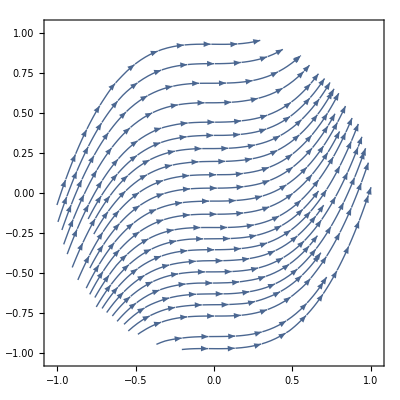

```mathematica
StreamPlot[
{1,3 x^2},
{x,y}∈Disk[]]
```

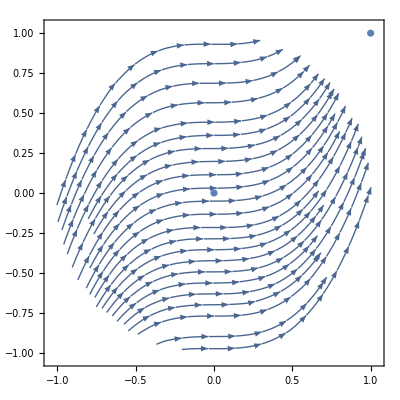

```mathematica
Show[{
StreamPlot[
{1,3 x^2},
{x,y}∈Disk[]],
ListPlot[{{0,0},{1,1}}]
}]
```

```mathematica
FullSimplify[1,x∈Real
```

```mathematica
Reals
```

ℝ

```mathematica
FullSimplify[
Normalize[{1,g'[x]}].
Normalize[{1,f[x]}]==0
,{x,f[x],g[x],f'[x],g'[x]}∈Reals]
```

1+f[x] g'[x]==0

```mathematica
DSolve[1+f[x] g'[x]==0,f[x],x]
```

{{f[x]→-1/g'[x]}}

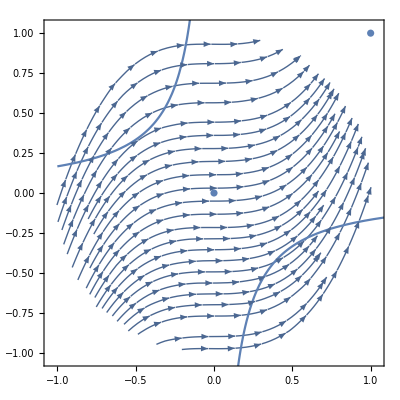

```mathematica
Show[{
StreamPlot[
{1,3 x^2},
{x,y}∈Disk[]],
ListPlot[{{0,0},{1,1}}],
Plot[-1/(6x),{x,-1,2}]
}]
```

```mathematica
With[{g=Function[x,3 x^2]},
-1/g'[x]]
```

-1/(6 x)

```mathematica
With[{g=Function[x,x^3]},
-1/g'[x]]
```

-1/(3 x^2)

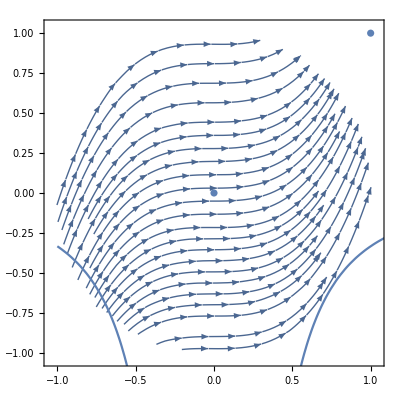

```mathematica
Show[{
StreamPlot[
{1,3 x^2},
{x,y}∈Disk[]],
ListPlot[{{0,0},{1,1}}],
Plot[-1/(3 x^2),{x,-1,2}]
}]
```

```mathematica
FullSimplify[
Normalize[{1,g'[x]}].
Normalize[{1,f[x]}]==1
,{x,f[x],g[x],f'[x],g'[x]}∈Reals]
```

√((1+f[x]^2) (1+g'[x]^2))==1+f[x] g'[x]

```mathematica
Solve[√((1+f[x]^2) (1+g'[x]^2))==1+f[x] g'[x],f[x],x]
```

Solve::bdomv: Warning: x is not a valid domain specification. Assuming it is a variable to eliminate.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{}}

```mathematica
DSolve[√((1+f[x]^2) (1+g'[x]^2))==1+f[x] g'[x],f[x],x]
```

{{f[x]→g'[x]}}

```mathematica
With[{g=Function[x,x^3]},
g'[x]]
```

3 x^2

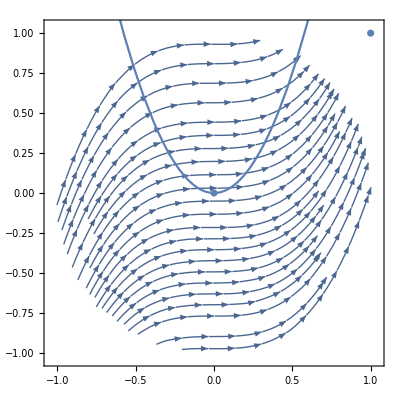

```mathematica
Show[{
StreamPlot[
{1,3 x^2},
{x,y}∈Disk[]],
ListPlot[{{0,0},{1,1}}],
Plot[3 x^2,{x,-1,2}]
}]
```

```mathematica
DSolve[√((1+f[x]^2) (1+g'[x]^2))==1+f[x] g'[x],f[x],x]
```

```mathematica
FullSimplify[
Normalize[{1,3 x^2}].
Normalize[{1,f[x]}]==1
,{x,f[x],f'[x]}∈Reals]
```

√((1+9 x^4) (1+f[x]^2))==1+3 x^2 f[x]

```mathematica
Reduce[√((1+9 x^4) (1+f[x]^2))==1+3 x^2 f[x]]
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[√((1+9 x^4) (1+f[x]^2))==1+3 x^2 f[x]]

```mathematica
DSolve[√((1+9 x^4) (1+f[x]^2))==1+3 x^2 f[x],f[x],x]
```

{{f[x]→3 x^2}}

```mathematica
FullSimplify[
Normalize[{1,3 x^2}].
Normalize[{1,f'[x]}]==1
,{x,f[x],f'[x]}∈Reals]
```

√((1+9 x^4) (1+f'[x]^2))==1+3 x^2 f'[x]

```mathematica
DSolve[√((1+9 x^4) (1+f'[x]^2))==1+3 x^2 f'[x],f[x],x]
```

{{f[x]→x^3+C[1]}}

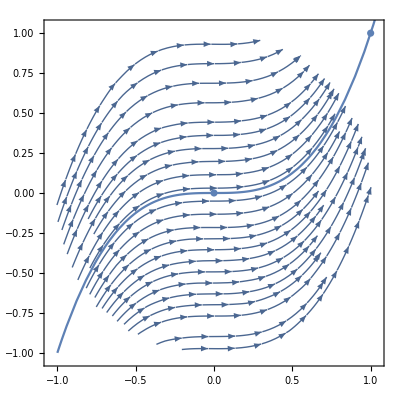

```mathematica
Show[{
StreamPlot[
{1,3 x^2},
{x,y}∈Disk[]],
ListPlot[{{0,0},{1,1}}],
Plot[x^3,{x,-1,2}]
}]
```

```mathematica
FullSimplify[
Normalize[{1,3 x^2}].
Normalize[{1,f'[x]}]==1
,{x,f[x],f'[x]}∈Reals]
```

```mathematica
x==1+x^2
```

x==1+x^2

```mathematica
Reduce[x==1+x^2]
```

x==(-1)^(1/3)||x==-(-1)^(2/3)

```mathematica
Trace[Reduce[x==1+x^2]]
```

{Reduce[x==1+x^2],x==(-1)^(1/3)||x==-(-1)^(2/3)}

```mathematica
SurfaceData[]
```

{astroidal ellipsoid,Barth decic surface,Barth sextic surface,Berg surface,Bohemian dome,Bour minimal surface,Boy surface,buggle surface,calypso surface,calyx surface,capsule,Cassini surface,Catalan surface,catenoid,Cayley cubic (Hunt parametrization),Cayley cubic (Endraß parametrization),Hessian of the Cayley cubic,Banchoff's Chmutov-like surface,citrus surface,Clebsch diagonal cubic,columpius surface,infinite cone,closed cone,finite cone,conical frustum,corkscrew surface,corner cushion surface,cornucopia surface,Costa minimal surface,crixxi surface,cross-cap,crossed trough,cross surface,cube surface,cuboid surface,cushion surface,infinite cylinder,closed cylinder,finite cylinder,finite horizontal cylindrical segment,daisy surface,dance surface,date surface,dervish surface,diabolo surface,ding-dong surface,Dini surface,double sphere,dromedary surface,eight surface,ellipsoid,infinite elliptic cone,finite elliptic cone,infinite elliptic cylinder,finite elliptic cylinder,elliptic helicoid,one-sheeted elliptic hyperboloid,two-sheeted elliptic hyperboloid,elliptic paraboloid,elliptic torus,first Endraß octic,second Endraß octic,Enneper minimal surface,eve surface,fanfare surface,flirt surface,first funnel surface,second funnel surface,Gabriel's horn,geisha surface,Goursat surface,handkerchief surface,harlequin surface,Taubin's heart surface,heaven-and-hell surface,helicoid,helix surface,hemisphere,Henneberg minimal surface,Herz surface,horn torus,Hunt surface,hyperbolic cylinder,hyperbolic helicoid,hyperbolic octahedron,hyperbolic paraboloid,one-sheeted hyperboloid,two-sheeted hyperboloid,Eistüte surface,jack-o'-lantern face surface,kiss surface,figure-eight parametrization of the Klein bottle,Klein quartic surface,kolibri surface,Kuen surface,Labs septic surface,Leopold surface,Lichtenfels surface,limão surface,lip surface,Menn surface,meow surface,Michelangelo surface,miter surface,Möbius strip,monkey saddle,mushroom surface,Nepali surface,Nordstrand weird surface,oloid,parabolic cylinder,infinite paraboloid,paraboloidal segment,Peano surface,peninsula surface,pigeon surface,pipe surface,piriform surface,plane,plop surface,Plücker conoid,pseudosphere,pumpkin surface,quartoid,Rembs surface,Roman surface,rounded cube surface,saddle surface,Sarti dodecic surface,Scherk's first minimal surface,Scherk's second minimal surface,sea horse surface,seashell surface,see-through surface,shoe surface,Sievert surface,sine surface,smiley face surface,snowflake surface,solitude surface,sphere,spherical cap,spheroid,spitz surface,square pyramid surface,star surface,Steinbach screw,Steiner type-2 surface,Steiner type-4 surface,2-cylinder Steinmetz configuration,3-cylinder Steinmetz configuration,subway surface,superegg,superellipsoid,swallowtail surface,tanglecube,thistle surface,tobel surface,Togliatti surface,tooth surface,torispherical dome,torus,trinoid,twilight surface,two-holed surface,vis-à-vis surface,waggle surface,Wallis conical edge,Whitney umbrella,wigwam surface,wind tunnel surface,xano surface,zeppelin surface,zone}

```mathematica
SurfaceData["Sphere", "ParametricEquations"]
```

Function[a,Function[{u,v},a {Cos[u] Sin[v],Sin[u] Sin[v],Cos[v]}]]

```mathematica
Function[a,Function[{u,v},a {Cos[u] Sin[v],Sin[u] Sin[v],Cos[v]}]][a]
```

Function[{u$,v$},a {Cos[u$] Sin[v$],Sin[u$] Sin[v$],Cos[v$]}]

```mathematica
Function[a,Function[{u,v},a {Cos[u] Sin[v],Sin[u] Sin[v],Cos[v]}]][x]
```

Function[{u$,v$},x {Cos[u$] Sin[v$],Sin[u$] Sin[v$],Cos[v$]}]

```mathematica
{Cos[u] Sin[v],Sin[u] Sin[v],Cos[v]}
```

{Cos[u] Sin[v],Sin[u] Sin[v],Cos[v]}

```mathematica
ParametricPlot3D[{Cos[u] Sin[v],Sin[u] Sin[v],Cos[v]},{u,0,2π},{v,0,2π}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{u,v,0},{u,0,2π},{v,0,2π}]
```

-Graphics3D-

```mathematica
(1-a)p+a q/.{p->{u,v,0},q-> {Cos[u] Sin[v],Sin[u] Sin[v],Cos[v]}}
```

{(1-a) u+a Cos[u] Sin[v],(1-a) v+a Sin[u] Sin[v],a Cos[v]}

```mathematica
Manipulate[
ParametricPlot3D[
{(1-a) u+a Cos[u] Sin[v],(1-a) v+a Sin[u] Sin[v],a Cos[v]},
{u,0,2π},{v,0,2π}],
{a,0,1}]
```

```mathematica
(1-a)p+a q/.{p->{Cos[u],Sin[v],0},q-> {Cos[u] Sin[v],Sin[u] Sin[v],Cos[v]}}
```

{(1-a) Cos[u]+a Cos[u] Sin[v],(1-a) Sin[v]+a Sin[u] Sin[v],a Cos[v]}

```mathematica
Manipulate[
ParametricPlot3D[
{(1-a) Cos[u]+a Cos[u] Sin[v],(1-a) Sin[v]+a Sin[u] Sin[v],a Cos[v]}
,{u,0,2π},{v,0,2π}],
{a,0,1}]
```

```mathematica
ParametricPlot3D[{Cos@u,Sin@v,0},{u,0,2π},{v,0,2π}]
```

-Graphics3D-



```mathematica
ParametricPlot[{Cos@u,Sin@u},{u,0,2π}]
```

```mathematica
ParametricPlot3D[{Cos@u,Sin@u,0},{u,0,2π},{v,0,2π}]
```

-Graphics3D-

```mathematica
(1-a)p+a q/.{p->{Cos@u,Sin@u,0},q-> {Cos[u] Sin[v],Sin[u] Sin[v],Cos[v]}}
```

{(1-a) Cos[u]+a Cos[u] Sin[v],(1-a) Sin[u]+a Sin[u] Sin[v],a Cos[v]}

```mathematica
Manipulate[
ParametricPlot3D[
{(1-a) Cos[u]+a Cos[u] Sin[v],(1-a) Sin[u]+a Sin[u] Sin[v],a Cos[v]}
,{u,0,2π},{v,0,2π}],
{a,0,1}]
```

```mathematica
SurfaceData[]
```

{astroidal ellipsoid,Barth decic surface,Barth sextic surface,Berg surface,Bohemian dome,Bour minimal surface,Boy surface,buggle surface,calypso surface,calyx surface,capsule,Cassini surface,Catalan surface,catenoid,Cayley cubic (Hunt parametrization),Cayley cubic (Endraß parametrization),Hessian of the Cayley cubic,Banchoff's Chmutov-like surface,citrus surface,Clebsch diagonal cubic,columpius surface,infinite cone,closed cone,finite cone,conical frustum,corkscrew surface,corner cushion surface,cornucopia surface,Costa minimal surface,crixxi surface,cross-cap,crossed trough,cross surface,cube surface,cuboid surface,cushion surface,infinite cylinder,closed cylinder,finite cylinder,finite horizontal cylindrical segment,daisy surface,dance surface,date surface,dervish surface,diabolo surface,ding-dong surface,Dini surface,double sphere,dromedary surface,eight surface,ellipsoid,infinite elliptic cone,finite elliptic cone,infinite elliptic cylinder,finite elliptic cylinder,elliptic helicoid,one-sheeted elliptic hyperboloid,two-sheeted elliptic hyperboloid,elliptic paraboloid,elliptic torus,first Endraß octic,second Endraß octic,Enneper minimal surface,eve surface,fanfare surface,flirt surface,first funnel surface,second funnel surface,Gabriel's horn,geisha surface,Goursat surface,handkerchief surface,harlequin surface,Taubin's heart surface,heaven-and-hell surface,helicoid,helix surface,hemisphere,Henneberg minimal surface,Herz surface,horn torus,Hunt surface,hyperbolic cylinder,hyperbolic helicoid,hyperbolic octahedron,hyperbolic paraboloid,one-sheeted hyperboloid,two-sheeted hyperboloid,Eistüte surface,jack-o'-lantern face surface,kiss surface,figure-eight parametrization of the Klein bottle,Klein quartic surface,kolibri surface,Kuen surface,Labs septic surface,Leopold surface,Lichtenfels surface,limão surface,lip surface,Menn surface,meow surface,Michelangelo surface,miter surface,Möbius strip,monkey saddle,mushroom surface,Nepali surface,Nordstrand weird surface,oloid,parabolic cylinder,infinite paraboloid,paraboloidal segment,Peano surface,peninsula surface,pigeon surface,pipe surface,piriform surface,plane,plop surface,Plücker conoid,pseudosphere,pumpkin surface,quartoid,Rembs surface,Roman surface,rounded cube surface,saddle surface,Sarti dodecic surface,Scherk's first minimal surface,Scherk's second minimal surface,sea horse surface,seashell surface,see-through surface,shoe surface,Sievert surface,sine surface,smiley face surface,snowflake surface,solitude surface,sphere,spherical cap,spheroid,spitz surface,square pyramid surface,star surface,Steinbach screw,Steiner type-2 surface,Steiner type-4 surface,2-cylinder Steinmetz configuration,3-cylinder Steinmetz configuration,subway surface,superegg,superellipsoid,swallowtail surface,tanglecube,thistle surface,tobel surface,Togliatti surface,tooth surface,torispherical dome,torus,trinoid,twilight surface,two-holed surface,vis-à-vis surface,waggle surface,Wallis conical edge,Whitney umbrella,wigwam surface,wind tunnel surface,xano surface,zeppelin surface,zone}

```mathematica
(1-a)p+a q/.{p->{Cos@u,Sin@u,0},q-> {Cos[u] Sin[v],Sin[u] Sin[v],Cos[v]}}
```

```mathematica
SurfaceData["Torus", "ParametricEquations"]
```

EntityValue::timeout: A network operation for EntityValue timed out. Please try again later.

Missing[RetrievalFailure]

```mathematica
SurfaceData["Torus", "ParametricEquations"]
```

Function[{a,c},Function[{u,v},{(c+a Cos[v]) Cos[u],(c+a Cos[v]) Sin[u],a Sin[v]}]]

```mathematica
Function[{u,v},{(c+a Cos[v]) Cos[u],(c+a Cos[v]) Sin[u],a Sin[v]}]/.{u-> u,v->v}
```

Function[{u,v},{(c+a Cos[v]) Cos[u],(c+a Cos[v]) Sin[u],a Sin[v]}]

```mathematica
{(c+a Cos[v]) Cos[u],(c+a Cos[v]) Sin[u],a Sin[v]} /.{u-> u,v->v}
```

{Cos[u] (c+a Cos[v]),(c+a Cos[v]) Sin[u],a Sin[v]}

```mathematica
{(c+a Cos[v]) Cos[u],(c+a Cos[v]) Sin[u],a Sin[v]} /.{u-> u,v->v,a->1,c->2}
```

{Cos[u] (2+Cos[v]),(2+Cos[v]) Sin[u],Sin[v]}

```mathematica
ParametricPlot3D[{Cos[u] (2+Cos[v]),(2+Cos[v]) Sin[u],Sin[v]},{u,0,2π},{v,0,2π}]
```

-Graphics3D-

```mathematica
(1-a)p+a q/.{p->{Cos[u] (2+Cos[v]),(2+Cos[v]) Sin[u],Sin[v]},q-> {Cos[u] Sin[v],Sin[u] Sin[v],Cos[v]}}
```

{(1-a) Cos[u] (2+Cos[v])+a Cos[u] Sin[v],(1-a) (2+Cos[v]) Sin[u]+a Sin[u] Sin[v],a Cos[v]+(1-a) Sin[v]}

```mathematica
Manipulate[
ParametricPlot3D[
{(1-a) Cos[u] (2+Cos[v])+a Cos[u] Sin[v],(1-a) (2+Cos[v]) Sin[u]+a Sin[u] Sin[v],a Cos[v]+(1-a) Sin[v]}
,{u,0,2π},{v,0,2π}],
{a,0,1}]
```

```mathematica
With[{p=RandomChoice[SurfaceData[]]},
p]
```

finite elliptic cylinder

```mathematica
With[{p=RandomChoice[SurfaceData[]]},
p
]
```

dromedary surface

```mathematica
With[{p=RandomChoice[SurfaceData[]],q=RandomChoice[SurfaceData[]]},
{p,q}
]
```

{Goursat surface,spheroid}

```mathematica
With[{p=RandomChoice[SurfaceData[]],q=RandomChoice[SurfaceData[]]},
{p->SurfaceData[p,"ParametricEquations"],q->SurfaceData[q,"ParametricEquations"]}
]
```

{columpius surface→Missing[NotAvailable],Menn surface→Function[a,Function[{u,v},{u,v,a u^4+u^2 v-v^2}]]}

```mathematica
With[{p=RandomChoice[SurfaceData[]],q=RandomChoice[SurfaceData[]]},
{p->SurfaceData[p,"ParametricEquations"],q->SurfaceData[q,"ParametricEquations"]}
]
```

{finite elliptic cylinder→Function[{a,b,h},Function[{u,v},{a Cos[u],b Sin[u],v}]],Plücker conoid→Function[{c,n},Function[{r,t},{r Cos[t],r Sin[t],c Sin[n t]}]]}

```mathematica
{ Cos[u], Sin[u],v}
```

{Cos[u],Sin[u],v}

```mathematica
{ Cos[u], Sin[u], Sin[2 u]}
```

{Cos[u],Sin[u],Sin[2 u]}

```mathematica
(1-a)p+a q/.{p-> { Cos[u], Sin[u],v},q-> {Cos[u],Sin[u],Sin[2 u]}}
```

{(1-a) Cos[u]+a Cos[u],(1-a) Sin[u]+a Sin[u],(1-a) v+a Sin[2 u]}

```mathematica
Manipulate[
ParametricPlot3D[
{(1-a) Cos[u]+a Cos[u],(1-a) Sin[u]+a Sin[u],(1-a) v+a Sin[2 u]}
,{u,0,2π},{v,0,2π}],
{a,0,1}]
```

```mathematica
(1-a)p+a q/.{p-> { Cos[u], Sin[u],v},q->  {Cos[u] Sin[v],Sin[u] Sin[v],Cos[v]}}
```

{(1-a) Cos[u]+a Cos[u] Sin[v],(1-a) Sin[u]+a Sin[u] Sin[v],(1-a) v+a Cos[v]}

```mathematica
Manipulate[
ParametricPlot3D[
{(1-a) Cos[u]+a Cos[u] Sin[v],(1-a) Sin[u]+a Sin[u] Sin[v],(1-a) v+a Cos[v]}
,{u,0,2π},{v,0,2π}],
{a,0,1}]
```

```mathematica
With[{
p= {Cos[u],Sin[u],Sin[2 u]},
q={Cos[u] Sin[v],Sin[u] Sin[v],Cos[v]}
},
With[{homotopy=(1-a)p+a q},
Manipulate[
ParametricPlot3D[
homotopy
,{u,0,2π},{v,0,2π}],
{a,0,1}]
]]
```

```mathematica
{(1-a) Cos[u]+a Cos[u] Sin[v],(1-a) Sin[u]+a Sin[u] Sin[v],(1-a) v+a Cos[v]}{Cos[u] Sin[v],Sin[u] Sin[v],Cos[v]}
```

{Cos[u] Sin[v] ((1-a) Cos[u]+a Cos[u] Sin[v]),Sin[u] Sin[v] ((1-a) Sin[u]+a Sin[u] Sin[v]),Cos[v] ((1-a) v+a Cos[v])}

```mathematica
FullSimplify[
Normalize@{(1-a) Cos[u]+a Cos[u] Sin[v],(1-a) Sin[u]+a Sin[u] Sin[v],(1-a) v+a Cos[v]}.
Normalize@{Cos[u] Sin[v],Sin[u] Sin[v],Cos[v]},
{a,u,v}∈Reals∧0≤a≤1∧0≤u≤2π∧0≤v≤2π]
```

(a-(-1+a) v Cos[v]+Sin[v]-a Sin[v])/(√(1-2 a+2 a^2+(-1+a)^2 v^2-2 (-1+a) a (v Cos[v]+Sin[v])))

```mathematica
Plot3D[(a-(-1+a) v Cos[v]+Sin[v]-a Sin[v])/(√(1-2 a+2 a^2+(-1+a)^2 v^2-2 (-1+a) a (v Cos[v]+Sin[v]))),{a,0,1},{v,0,2π}]
```

-Graphics3D-

```mathematica
Reals
```

ℝ

```mathematica
With[{
p= {Cos[u],Sin[u],Sin[2 u]},
q={Cos[u] Sin[v],Sin[u] Sin[v],Cos[v]}
},
With[{homotopy=(1-a)p+a q},
Manipulate[
ParametricPlot3D[
homotopy
,{u,0,2π},{v,0,2π}],
{a,0,1}]
]]
```

```mathematica
SurfaceData[Entity["Surface","GabrielsHorn"],"ParametricEquations"]
```

EntityValue::timeout: A network operation for EntityValue timed out. Please try again later.

Missing[RetrievalFailure]

```mathematica
SurfaceData[Entity["Surface","GabrielsHorn"],"ParametricEquations"]
```

EntityValue::timeout: A network operation for EntityValue timed out. Please try again later.

Missing[RetrievalFailure]

```mathematica
SurfaceData[Entity["Surface","GabrielsHorn"],"ParametricEquations"]
```

EntityValue::timeout: A network operation for EntityValue timed out. Please try again later.

Missing[RetrievalFailure]

```mathematica
SurfaceData[]
```

{astroidal ellipsoid,Barth decic surface,Barth sextic surface,Berg surface,Bohemian dome,Bour minimal surface,Boy surface,buggle surface,calypso surface,calyx surface,capsule,Cassini surface,Catalan surface,catenoid,Cayley cubic (Hunt parametrization),Cayley cubic (Endraß parametrization),Hessian of the Cayley cubic,Banchoff's Chmutov-like surface,citrus surface,Clebsch diagonal cubic,columpius surface,infinite cone,closed cone,finite cone,conical frustum,corkscrew surface,corner cushion surface,cornucopia surface,Costa minimal surface,crixxi surface,cross-cap,crossed trough,cross surface,cube surface,cuboid surface,cushion surface,infinite cylinder,closed cylinder,finite cylinder,finite horizontal cylindrical segment,daisy surface,dance surface,date surface,dervish surface,diabolo surface,ding-dong surface,Dini surface,double sphere,dromedary surface,eight surface,ellipsoid,infinite elliptic cone,finite elliptic cone,infinite elliptic cylinder,finite elliptic cylinder,elliptic helicoid,one-sheeted elliptic hyperboloid,two-sheeted elliptic hyperboloid,elliptic paraboloid,elliptic torus,first Endraß octic,second Endraß octic,Enneper minimal surface,eve surface,fanfare surface,flirt surface,first funnel surface,second funnel surface,Gabriel's horn,geisha surface,Goursat surface,handkerchief surface,harlequin surface,Taubin's heart surface,heaven-and-hell surface,helicoid,helix surface,hemisphere,Henneberg minimal surface,Herz surface,horn torus,Hunt surface,hyperbolic cylinder,hyperbolic helicoid,hyperbolic octahedron,hyperbolic paraboloid,one-sheeted hyperboloid,two-sheeted hyperboloid,Eistüte surface,jack-o'-lantern face surface,kiss surface,figure-eight parametrization of the Klein bottle,Klein quartic surface,kolibri surface,Kuen surface,Labs septic surface,Leopold surface,Lichtenfels surface,limão surface,lip surface,Menn surface,meow surface,Michelangelo surface,miter surface,Möbius strip,monkey saddle,mushroom surface,Nepali surface,Nordstrand weird surface,oloid,parabolic cylinder,infinite paraboloid,paraboloidal segment,Peano surface,peninsula surface,pigeon surface,pipe surface,piriform surface,plane,plop surface,Plücker conoid,pseudosphere,pumpkin surface,quartoid,Rembs surface,Roman surface,rounded cube surface,saddle surface,Sarti dodecic surface,Scherk's first minimal surface,Scherk's second minimal surface,sea horse surface,seashell surface,see-through surface,shoe surface,Sievert surface,sine surface,smiley face surface,snowflake surface,solitude surface,sphere,spherical cap,spheroid,spitz surface,square pyramid surface,star surface,Steinbach screw,Steiner type-2 surface,Steiner type-4 surface,2-cylinder Steinmetz configuration,3-cylinder Steinmetz configuration,subway surface,superegg,superellipsoid,swallowtail surface,tanglecube,thistle surface,tobel surface,Togliatti surface,tooth surface,torispherical dome,torus,trinoid,twilight surface,two-holed surface,vis-à-vis surface,waggle surface,Wallis conical edge,Whitney umbrella,wigwam surface,wind tunnel surface,xano surface,zeppelin surface,zone}

```mathematica
SurfaceData[Entity["Surface","TogliattiSurface"],"ParametricEquations"]
```

Missing[NotAvailable]

```mathematica
Select[SurfaceData[],Not@MissingQ@SurfaceData[#,"ParametricEquations"]&]
```

{astroidal ellipsoid,Bohemian dome,Bour minimal surface,Boy surface,Catalan surface,catenoid,infinite cone,finite cone,conical frustum,corkscrew surface,cornucopia surface,Costa minimal surface,cross-cap,crossed trough,infinite cylinder,finite cylinder,finite horizontal cylindrical segment,ding-dong surface,Dini surface,double sphere,eight surface,ellipsoid,infinite elliptic cone,finite elliptic cone,infinite elliptic cylinder,finite elliptic cylinder,elliptic helicoid,one-sheeted elliptic hyperboloid,elliptic paraboloid,elliptic torus,Enneper minimal surface,first funnel surface,Gabriel's horn,handkerchief surface,helicoid,hemisphere,Henneberg minimal surface,horn torus,hyperbolic helicoid,hyperbolic octahedron,hyperbolic paraboloid,one-sheeted hyperboloid,two-sheeted hyperboloid,jack-o'-lantern face surface,kiss surface,figure-eight parametrization of the Klein bottle,Kuen surface,Lichtenfels surface,Menn surface,Möbius strip,monkey saddle,parabolic cylinder,infinite paraboloid,paraboloidal segment,Peano surface,Plücker conoid,pseudosphere,pumpkin surface,quartoid,Rembs surface,Roman surface,rounded cube surface,Scherk's first minimal surface,Scherk's second minimal surface,seashell surface,shoe surface,Sievert surface,sine surface,smiley face surface,sphere,spherical cap,spheroid,Steinbach screw,swallowtail surface,torus,trinoid,Wallis conical edge,Whitney umbrella,zone}

```mathematica
SurfaceData[Entity["Surface","Zone"],"Properties"]
```

{algebraic degree,algebraic equation,alternate names,area element,associated people,Cartesian equation,centroid of solid,Christoffel symbol of the second kind,(map) chromatic number,classes,cross sections,entity classes,Euler characteristic,filled region,coefficients of the first fundamental form,Gaussian curvature,generalized diameter,genus,3-D graphics,image,implicit Gaussian curvature,implicit mean curvature,implicit normal vector,moment of inertia tensor of solid,CDF of lengths,mean line segment length,PDF of lengths,mean curvature,metric tensor,name,number of nodes,normal vector,parameters,parametric equations,principal curvatures,number of punctures,related Wolfram Language symbols,Ricci tensor,Riemann tensor,coefficients of the second fundamental form,semialgebraic description,singular points,sport objects,surface area,variable constraints,variable descriptions,variables,vector length,volume of solid}

```mathematica
Select[SurfaceData[],Not@MissingQ@SurfaceData[#,EntityProperty["Surface","Graphics3D"]]&]
```

EntityValue::timeout: A network operation for EntityValue timed out. Please try again later.

General::stop: Further output of EntityValue::timeout will be suppressed during this calculation.

EntityValue::ctimeout: A computation timed out.

{astroidal ellipsoid,Barth decic surface,Barth sextic surface,Berg surface,Bohemian dome,Bour minimal surface,Boy surface,buggle surface,Cayley cubic (Hunt parametrization),Cayley cubic (Endraß parametrization),Hessian of the Cayley cubic,Banchoff's Chmutov-like surface,citrus surface,Clebsch diagonal cubic,columpius surface,infinite cone,closed cone,finite cone,conical frustum,corkscrew surface,corner cushion surface,cornucopia surface,Costa minimal surface,crixxi surface,cross-cap,crossed trough,cross surface,cube surface,cuboid surface,cushion surface,infinite cylinder,closed cylinder,finite cylinder,finite horizontal cylindrical segment,daisy surface,dance surface,date surface,dervish surface,diabolo surface,ding-dong surface,Dini surface,double sphere,dromedary surface,eight surface,ellipsoid,infinite elliptic cone,finite elliptic cone,infinite elliptic cylinder,finite elliptic cylinder,elliptic helicoid,one-sheeted elliptic hyperboloid,two-sheeted elliptic hyperboloid,elliptic paraboloid,elliptic torus,first Endraß octic,second Endraß octic,Enneper minimal surface,eve surface,fanfare surface,flirt surface,first funnel surface,second funnel surface,Gabriel's horn,geisha surface,Goursat surface,handkerchief surface,harlequin surface,Taubin's heart surface,heaven-and-hell surface,helicoid,helix surface,hemisphere,Henneberg minimal surface,Herz surface,horn torus,Hunt surface,hyperbolic cylinder,hyperbolic helicoid,hyperbolic octahedron,hyperbolic paraboloid,one-sheeted hyperboloid,two-sheeted hyperboloid,Eistüte surface,kiss surface,figure-eight parametrization of the Klein bottle,Klein quartic surface,kolibri surface,Kuen surface,Labs septic surface,Leopold surface,Lichtenfels surface,limão surface,lip surface,Menn surface,meow surface,Michelangelo surface,miter surface,Möbius strip,monkey saddle,mushroom surface,Nepali surface,Nordstrand weird surface,oloid,parabolic cylinder,infinite paraboloid,paraboloidal segment,Peano surface,peninsula surface,pigeon surface,pipe surface,piriform surface,plane,plop surface,Plücker conoid,pseudosphere,pumpkin surface,quartoid,Rembs surface,Roman surface,rounded cube surface,saddle surface,Scherk's first minimal surface,Scherk's second minimal surface,sea horse surface,seashell surface,see-through surface,sphere,spherical cap,spheroid,spitz surface,square pyramid surface,star surface,Steinbach screw,Steiner type-2 surface,Steiner type-4 surface,2-cylinder Steinmetz configuration,3-cylinder Steinmetz configuration,subway surface,superegg,superellipsoid,swallowtail surface,tanglecube,thistle surface,tobel surface,Togliatti surface,tooth surface,torispherical dome,torus,trinoid,twilight surface,two-holed surface,vis-à-vis surface,waggle surface,Wallis conical edge,Whitney umbrella,wigwam surface,wind tunnel surface,xano surface,zeppelin surface,zone}

```mathematica
SurfaceData[Entity["Surface","SteinbachScrew"],"ParametricEquations"]
```

Function[a,Function[{u,v},a {u Cos[v],u Sin[v],v Cos[u]}]]

```mathematica
With[{
p={u Cos[v],u Sin[v],v Cos[u]},
q={Cos[u] Sin[v],Sin[u] Sin[v],Cos[v]}
},
With[{homotopy=(1-a)p+a q},
Manipulate[
ParametricPlot3D[
homotopy
,{u,0,2π},{v,0,2π}],
{a,0,1}]
]]
```

```mathematica
Options[Manipulate]
```

{Alignment→Automatic,AppearanceElements→Automatic,AutoAction→False,AutorunSequencing→Automatic,BaselinePosition→Automatic,BaseStyle→{},Bookmarks→{},ContentSize→Automatic,ContinuousAction→Automatic,ControlAlignment→Automatic,ControllerLinking→Automatic,ControllerMethod→Automatic,ControllerPath→Automatic,ControlPlacement→Automatic,ControlType→Automatic,DefaultBaseStyle→Manipulate,DefaultLabelStyle→ManipulateLabel,Deinitialization:>None,Deployed→False,Evaluator→Automatic,Frame→False,FrameLabel→None,FrameMargins→Automatic,ImageMargins→0,Initialization:>None,InterpolationOrder→Automatic,LabelStyle→{},LocalizeVariables→True,Method→{},Paneled→True,PreserveImageOptions→True,RotateLabel→False,SaveDefinitions→False,ShrinkingDelay→0,SynchronousInitialization→True,SynchronousUpdating→Automatic,TouchscreenAutoZoom→False,TouchscreenControlPlacement→Automatic,TrackedSymbols→Full,UndoTrackedVariables:>None,UnsavedVariables:>None,UntrackedVariables:>None}

```mathematica
man=Manipulate[Plot[Sin[x],{x,0,end},ImageSize->{500,250}],{end,Pi,2 Pi,0.1,Appearance->"Open"},ContentSize->550]
```

```mathematica
Export[man,"GIF"]
```

Export::chtype: First argument  is not a valid file specification.

$Failed

```mathematica
Export["graph.gif",man]
```

graph.gif

```mathematica
ExpandFileName["graph.gif"]
```

/home/sguzman/graph.gif

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["graph.gif"]]]
```

```mathematica
MemoryInUse[]
```

396306984

```mathematica
Export["steinbach_crew_to_sphere_linear_homotopy.gif",With[{
p={u Cos[v],u Sin[v],v Cos[u]},
q={Cos[u] Sin[v],Sin[u] Sin[v],Cos[v]}
},
With[{homotopy=(1-a)p+a q},
Manipulate[
ParametricPlot3D[
homotopy
,{u,0,2π},{v,0,2π}],
{a,0,1}]
]]]
```

steinbach_crew_to_sphere_linear_homotopy.gif

```mathematica
MemoryInUse[]
```

397596064

```mathematica
(1-a)p+a q
```

(1-a) p+a q

```mathematica
(1-a) p+a q/.{p->{u,u},q->{Cos[u],Sin[u]}}
```

{(1-a) u+a Cos[u],(1-a) u+a Sin[u]}

```mathematica
ParametricPlot[
{(1-a) u+a Cos[u],(1-a) u+a Sin[u]},
{u,0,2π}]
```

-Graphics-

```mathematica
Manipulate[
ParametricPlot[
{(1-a) u+a Cos[u],(1-a) u+a Sin[u]},
{u,0,2π}],
{a,0,1}]
```

```mathematica
PDF[NormalDistribution[],x]
```

(ⅇ^(-x^2/2))/(√(2 π))

```mathematica
ⅇ^(-x^2/2)
```

ⅇ^(-x^2/2)

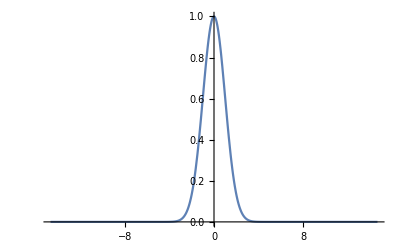

```mathematica
Plot[ⅇ^(-x^2/2),{x,-14.696938456699069,14.696938456699069},PlotRange->Full]
```

```mathematica
ⅇ^(-(1+x)^2/2)
```

ⅇ^(-1/2 (1+x)^2)

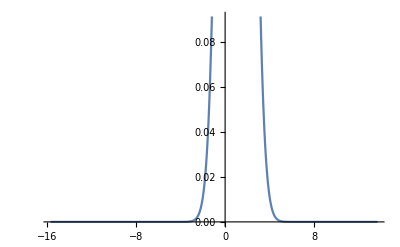

```mathematica
Plot[ⅇ^(-1/2 (x-1)^2),{x,-15.696938456699069,13.696938456699069}]
```

```mathematica
Manipulate[
Plot[
{x,x^2,(1-ⅇ^(-1/2 (x-a)^2))x+ⅇ^(-1/2 (x-a)^2)x^2},
{x,-2,2},PlotLegends->"Expressions"],
{a,0,1}]
```

```mathematica
Manipulate[
Plot[
{x,x^2,(1-ⅇ^(-1/2 (x-a)^2))x+ⅇ^(-1/2 (x-a)^2)x^2},
{x,-2,2},PlotLegends->"Expressions"],
{a,-2,2}]
```

```mathematica
1==∫_0^a x^2 ⅆx
```

1==a^3/3

```mathematica
Reduce[1==a^3/3]
```

a==-(-3)^(1/3)||a==3^(1/3)||a==(-1)^(2/3) 3^(1/3)

```mathematica
1==∫_0^a √(1+4 x^2)ⅆx
```

ConditionalExpression[1==1/4 (2 a √(1+4 a^2)+ArcSinh[2 a]),Re[a]≠0||-1/2<Im[a]<0||0<Im[a]<1/2]

```mathematica
FullSimplify[1==∫_0^a √(1+4 x^2)ⅆx,a∈Reals∧a>0]
```

2 a √(1+4 a^2)+ArcSinh[2 a]==4

```mathematica
Reduce[2 a √(1+4 a^2)+ArcSinh[2 a]==4]
```

Reduce[2 a √(1+4 a^2)+ArcSinh[2 a]==4]

```mathematica
NSolve[2 a √(1+4 a^2)+ArcSinh[2 a]==4,a,Reals]
```

{{a→0.763927}}

```mathematica
0.763926663317091^2
```

0.583584

```mathematica
f[x+α]==
```

```mathematica
Manipulate[
ParametricPlot[
{(1-a) u+a Cos[u],(1-a) u+a Sin[u]},
{u,0,2π}],
{a,0,1}]
```

```mathematica
(1-ⅇ^(-1/2 (1-a)^2)) p+ⅇ^(-1/2 (1-a)^2)q/.{p->{u,u},q->{Cos[u],Sin[u]}}
```

{(1-ⅇ^(-1/2 (1-a)^2)) u+ⅇ^(-1/2 (1-a)^2) Cos[u],(1-ⅇ^(-1/2 (1-a)^2)) u+ⅇ^(-1/2 (1-a)^2) Sin[u]}

```mathematica
Manipulate[
ParametricPlot[
{(1-ⅇ^(-1/2 (1-a)^2)) u+ⅇ^(-1/2 (1-a)^2) Cos[u],(1-ⅇ^(-1/2 (1-a)^2)) u+ⅇ^(-1/2 (1-a)^2) Sin[u]},
{u,0,2π}],
{a,0,2π}]
```

```mathematica
(1-x) p +x q
```

p (1-x)+q x

```mathematica
Manipulate[Plot[p (1-x)+q x,{x,-4.666666666666667,4.666666666666667}],{p,-6.,6.},{q,-2,2}]
```

```mathematica
p (1-x)+q x/.{p->x,q->x^2}
```

(1-x) x+x^3

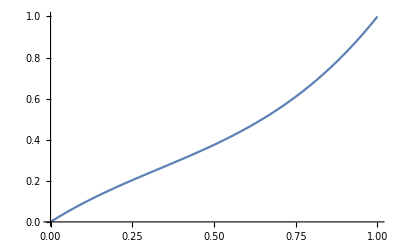

```mathematica
Plot[(1-x) x+x^3,{x,0,1}]
```

```mathematica
FullSimplify[
Normalize@{x,(1-x) x+x^3}.
Normalize@{x,x},x∈Reals]
```

(2+(-1+x) x)/(√2 √((2+(-2+x) x) (1+x^2)))

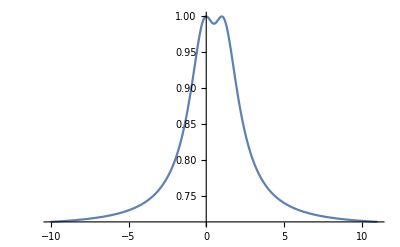

```mathematica
Plot[(2+(-1+x) x)/(√2 √((2+(-2+x) x) (1+x^2))),{x,-10.015555555555554,11.015555555555554}]
```

```mathematica
FullSimplify[
Normalize@{x,(1-x) x+x^3}.
Normalize@{x,x^2},x∈Reals]
```

(1+x-x^2+x^3)/(√(2+(-2+x) x) (1+x^2))

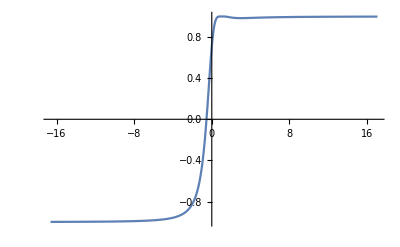

```mathematica
Plot[(1+x-x^2+x^3)/(√(2+(-2+x) x) (1+x^2)),{x,-16.628928524943472,17.08523951225139}]
```

```mathematica
RevolutionPlot3D[x,{x,0,1}]
```

-Graphics3D-

```mathematica
Manipulate[
RevolutionPlot3D[a x,{x,0,1}],
{a,0,1}]
```

```mathematica
Options@RevolutionPlot3D
```

{AlignmentPoint→Center,AspectRatio→Automatic,AutomaticImageSize→False,Axes→True,AxesEdge→Automatic,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},BoundaryStyle→Automatic,Boxed→True,BoxRatios→Automatic,BoxStyle→{},ClipPlanes→None,ClipPlanesStyle→Automatic,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,ControllerLinking→Automatic,ControllerMethod→Automatic,ControllerPath→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},EvaluationMonitor→None,Exclusions→Automatic,ExclusionsStyle→None,FaceGrids→None,FaceGridsStyle→{},FormatType:>TraditionalForm,ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelingSize→Automatic,LabelStyle→{},Lighting→Automatic,MaxRecursion→Automatic,Mesh→Automatic,MeshFunctions→{#4&,#5&},MeshShading→None,MeshStyle→Automatic,Method→Automatic,NormalsFunction→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotLabels→None,PlotLegends→None,PlotPoints→Automatic,PlotRange→Automatic,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotStyle→Automatic,PlotTheme:>$PlotTheme,PreserveImageOptions→Automatic,Prolog→{},RegionFunction→(True&),RevolutionAxis→{0,0,1},RotationAction→Fit,SphericalRegion→False,TextureCoordinateFunction→Automatic,TextureCoordinateScaling→True,Ticks→Automatic,TicksStyle→{},TouchscreenAutoZoom→False,ViewAngle→Automatic,ViewCenter→Automatic,ViewMatrix→Automatic,ViewPoint→{1.3,-2.4,2.},ViewProjection→Automatic,ViewRange→All,ViewVector→Automatic,ViewVertical→{0,0,1},WorkingPrecision→MachinePrecision}

```mathematica
Manipulate[
RevolutionPlot3D[(1-a) x+a x^2,{x,0,1}],
{a,0,1}]
```

```mathematica
Manipulate[
RevolutionPlot3D[(1-a) x+a (x^3-x),{x,0,1}],
{a,0,1}]
```

```mathematica
Manipulate[
RevolutionPlot3D[(1-a) x+a (x^3-Sin[x]),{x,0,1}],
{a,0,1}]
```

```mathematica
Manipulate[
RevolutionPlot3D[(1-a) x+a (Sin[10 x]),{x,0,1}],
{a,0,1}]
```

```mathematica
∫_0^(2π) √(x'[t]^2+y'[t]^2)ⅆt
```

∫_0^(2 π) √(x'[t]^2+y'[t]^2)ⅆt